# How to use the radial solutions?

Mathematica Notebook created by Andreas Möri on Thursday 19th November 2020
EPFL ENAC IIC GEL
GC B1 385 (Bâtiment GC)
Station 18, 1015 Lausanne, Switzerland
Phone: +41 (0)21 693 44 70
andreas.mori@epfl.ch
Geo-energy Laboratory EPFL

contributors:
Brice Lecampion  - brice.lecampion@epfl.ch
Carlo Peruzzo - carlo.peruzo@epfl.ch

version n.: 0.0.1

!!IMPORTANT!!!
Before running the script and exploring all functionalities please enter the directory guiding towards your folder with the paclets below in the section “We load the relevant packages” as paclet directory.

#### Formatting the way of plotting

```mathematica
(*http://szhorvat.net/pelican/latex-typesetting-in-mathematica.html*)
(*ResourceFunction["MaTeXInstall"][];*) (* <-Run  once forevere *) 
Needs["MaTeX`"]
Myfontsize=22;
texStyle={FontFamily->"CMU Serif",FontSize->Myfontsize};
SetOptions[Plot,Frame-> True,ImageSize-> 700,FrameStyle->Directive[Black],BaseStyle->texStyle];
SetOptions[LogLogPlot,Frame-> True,ImageSize-> 700,FrameStyle->Directive[Black],BaseStyle->texStyle];
SetOptions[ListPlot,Frame-> True,ImageSize-> 700,FrameStyle->Directive[Black],BaseStyle->texStyle];
SetOptions[ListLogPlot,Frame-> True,ImageSize-> 700,FrameStyle->Directive[Black],BaseStyle->texStyle];
SetOptions[ListLogLinearPlot,Frame-> True,ImageSize-> 700,FrameStyle->Directive[Black],BaseStyle->texStyle];
SetOptions[ListLogLogPlot,Frame-> True,ImageSize-> 700,FrameStyle->Directive[Black],BaseStyle->texStyle];
SetOptions[ListVectorPlot,Frame-> True,ImageSize-> 700,FrameStyle->Directive[Black],BaseStyle->texStyle];
SetOptions[ListLinePlot,Frame-> True,ImageSize-> 700,FrameStyle->Directive[Black],BaseStyle->texStyle];
```

#### We load the relevant packages

Setting up the path to the directory of the GitFolder. You’ll need to adapt this in your case!

```mathematica
pacletDirectory = "/Users/amoeri/Documents/Wolfram Mathematica/PyFrac_Mathematica_postprocessing"
PacletDirectoryLoad[pacletDirectory];
```

/Users/amoeri/Documents/Wolfram Mathematica/PyFrac_Mathematica_postprocessing

We simply load all the relevant packages. Based on this exercise

```mathematica
<<DescriptionUtilities`
<<NewtonianPulse`
<<RadialScaling`
<<ComputedSolutions`
<<PostProcessRadialPL`
<<RadialPowerLaw`
<<VertexSolutions`
```

#### Defining the set of parameters of your experiment

We define the parameters of our simulations.

For most of them we have two options.

Take for example the plain strain modulus  E'=E/(1-ν^2), you can either define in by directly passing E', or by seperately passing the Young’s modulus E as Emod (this is necessary as  E is protected by Mathematica as the Euler constant), and the Poisson’s ratio ν.

Similarly, you can provide directly the adapted fluid viscosity μ'=12 μ or simply the viscosity μ. The same principle goes for the other adapted parameters.

Note that if no fluid index n is provided the default value of n=1 is considered.

A note on the total injected volume Vo, this quantity can be entered either by giving simultaneously Qo and ts, or by directly passing Vo.

A final note is put on the fact that fore some scalings we would like to use directly KIc instead of K'. This is possible with an options which one can set to true. We will come back to this during the examples

```mathematica
paramSet1 = {KIc-> 1 10^6,Emod-> 10^9,ν-> .3,μ-> 10^-3,Qo-> 10^-2,ts-> 3600,Cl->10^-5}
paramSet2 = {Kp->  1 10^6,Ep->  10^9,μp-> 10^-3,Qo-> 10^-2,Vo-> 36,Cp-> 10^-5,n-> .75}
```

{KIc→1000000,Emod→1000000000,ν→0.3,μ→1/1000,Qo→1/100,ts→3600,Cl→1/100000}

{Kp→1000000,Ep→1000000000,μp→1/1000,Qo→1/100,Vo→36,Cp→1/100000,n→0.75}

We show here the outcome of the two parameter sets for the user to understand.

As to do so we load a part of the paclet normally hidden to the end user (as the details are not important

```mathematica
<<UtilityForScalings`
(* You see that the results adapt in function of your choice of input parameter.
Note that Mp = μ' *)
inputDataTransformation[paramSet1]
inputDataTransformation[paramSet2]
```

{Ep→1.0989×10^9,Vo→36,Qo→1/100,ts→3600,Mp→3/250,Kp→3.19154×10^6,Cp→1/50000,n→1}

{Ep→1000000000,Vo→ts/100,Qo→1/100,ts→ts,Mp→1/1000,Kp→1000000,Cp→1/100000,n→0.75}

```mathematica
(* And finally we give the option to use directly KIc as Kp by setting its boolean to true *)
inputDataTransformation[paramSet1,False]
```

{Ep→1.0989×10^9,Vo→36,Qo→1/100,ts→3600,Mp→3/250,Kp→1000000,Cp→1/50000,n→1}

#### Generalities

It is possible to get informations about every symbol and function that can by used by sympling entering a question mark ? in front of the function.

```mathematica
?toNumericalScaling
```

The parameter set defined previously will be generally used for this functions as an argument to pass. 

Further we would like to emphasize that generally four Vertexes are present and can be accessed as:
	- viscosity storage regime “M”
	- toughness storage regime “K”
	- viscosity leak-off regime “Mt”
	- toughness leak-off regime “Kt”
	
Scalings generally return the characteristic lengthscal Lstar, opening scale wstar, net pressure scale pstar, the flux scale qstar (only for viscosity related scalings) as well as the corresponding dimensionless numbers 𝒦 (dimensionless toughness), ℳ (dimensionless viscosity), 𝒞 (dimensionless leak-off coefficient) and 𝒱 (dimensionless storage coefficient)
	
We also have some near vertex solutions which can notably be accessed as:
	- toughness storage solution with first order viscosity “KVisc”
	- toughness storage solution with first order leak-off “KLeak”
	- toughness leak-off solution with first order storage “KtStor”
	
Generally it is always possible to get a scaling in it’s dimensionless form or in a dimensional form. As to do so a flag is implemented allowing you to decide which form do you need.

#### Recover a scaling in function of the parameters

It is often useful to recover a specific scaling in function of the parameters. This can simply be done by passing it the wished vertex (see generalities for the definitions), an empty parameter set and the (non defined!) variable t as time.

```mathematica
(* Displaying the characteristcal scales and the dimensionless parameters of the M-Vertex scaling *)
vertexScaling["M",{},t]
```

{Lstar→(Ep^(1/9) Qo^(1/3) t^(4/9))/μp^(1/9),wstar→(Qo^(1/3) t^(1/9) μp^(2/9))/Ep^(2/9),pstar→(Ep^(2/3) μp^(1/3))/t^(1/3),qstar→(Qo^(2/3) μp^(1/9))/(Ep^(1/9) t^(4/9)),𝒦→(Kp t^(1/9))/(Ep^(13/18) Qo^(1/6) μp^(5/18)),𝒞→(Cp Ep^(2/9) t^(7/18))/(Qo^(1/3) μp^(2/9))}

```mathematica
(* Displaying the characteristcal scales and the dimensionless parameters of the Kt-Vertex scaling *)
vertexScaling["Kt",{},t]
```

{Lstar→(√Qo t^(1/4))/(√Cp),wstar→(Kp Qo^(1/4) t^(1/8))/(Cp^(1/4) Ep),pstar→(Cp^(1/4) Kp)/(Qo^(1/4) t^(1/8)),qstar→(√Cp √Qo)/t^(1/4),ℳ→(√Cp Ep^3 √Qo μp)/(Kp^4 t^(1/4)),𝒱→(Cp^(5/4) Ep t^(3/8))/(Kp Qo^(1/4))}

```mathematica
(* The same is possible for the pulse (block injection) scalings *)
pulseVertexScalings["K",{},t]
pulseVertexScalings["Mt",{},t]
```

{Lstar→(Ep^(2/5) Vo^(2/5))/Kp^(2/5),wstar→(Kp^(4/5) Vo^(1/5))/Ep^(4/5),pstar→Kp^(6/5)/(Ep^(1/5) Vo^(1/5)),ℳ→(Ep^(13/5) Vo^(3/5) μp)/(Kp^(18/5) t),𝒞→(Cp Ep^(4/5) √t)/(Kp^(4/5) Vo^(1/5))}

{Lstar→(√Vo)/(√Cp t^(1/4)),wstar→(Vo^(3/8) μp^(1/4))/(Cp^(1/8) Ep^(1/4) t^(5/16)),pstar→(Cp^(3/8) Ep^(3/4) μp^(1/4))/(t^(1/16) Vo^(1/8)),𝒦→(Kp t^(3/16))/(Cp^(1/8) Ep^(3/4) Vo^(1/8) μp^(1/4)),𝒱→(Cp^(9/8) Ep^(1/4) t^(13/16))/(Vo^(3/8) μp^(1/4))}

#### Recover a vertex solution

We will now show you how to load the vertex solutions. First let’s consider an injection solution which is loaded by the following function.

```mathematica
?injectionVertexSolutions
```

The above gives you the way how to load it. We will perform this with our two parameter sets with two configuratios below.

```mathematica
injectionVertexSolutions["M",paramSet1,0.2,{1,70,635,10^3}]
```

{FractureLength→{2.48265,16.4043,43.7112,53.487},Opening→{0.000880582,0.00141183,0.0018038,0.00189716},NetPressure→{182718.,44335.2,21258.,18271.8}}

```mathematica
injectionVertexSolutions["Kt",paramSet2,0.7,10^2,False,False]
```

{FractureLength→(√2)/π,Opening→0.563772,NetPressure→0.684538}

The first parameter passed is the regime (see generalities for the options), the second is the set of parameters, the third is the dimensionless position within the fracture ρ (we will describe this below), the fourth the time at which we consider the solution (either a list or a single value). 

The fifth and sixth entrie are obtional booleans. If the fifth is set to false you will get the dimensionless solution (as default you get the dimensional solution). If the sixth is set to False we will use KIc directly instead of transforming it to K’.

The output given is the FractureLength (the radius of the fracture or the prefactor if dimensionless), Opening (at the ρ given) and the NetPressure (also given at ρ).

Plotting a profile

We will now give a definition of ρ and detail what we mean by dimensionless solutions. As such we are plotting the profile of the opening of a viscosity leak-off dominated fracture in function of the normalized x coordinate (along R) which is the definition of ρ = x/R.

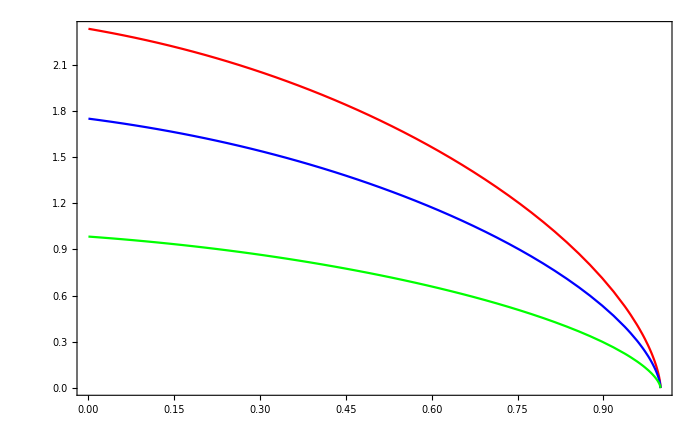
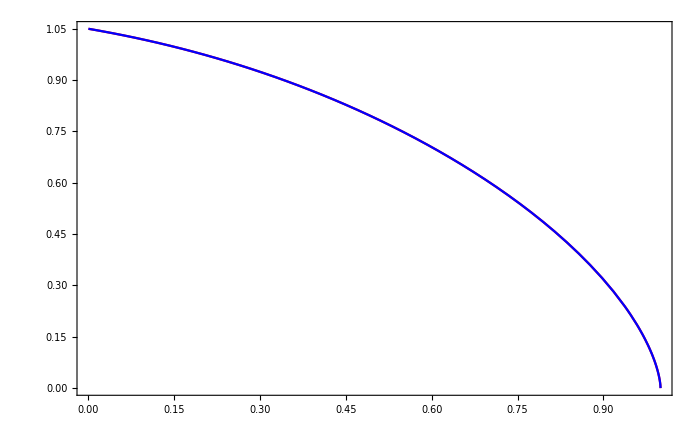

```mathematica
{Show[Plot[Opening  10^3/.injectionVertexSolutions["Mt",paramSet1,ρ,10^4],{ρ,0,1},PlotStyle->Red,PlotLegends->{MaTeX[" t=10\\textsuperscript{4} ",FontSize->Myfontsize-2]}],
Plot[Opening 10^3/.injectionVertexSolutions["Mt",paramSet1,ρ,10^2],{ρ,0,1},PlotStyle->Blue,PlotLegends->{MaTeX[" t=10\\textsuperscript{2} ",FontSize->Myfontsize-2]}],
Plot[Opening 10^3/.injectionVertexSolutions["Mt",paramSet1,ρ,10^-2],{ρ,0,1},PlotStyle->Green,PlotLegends->{MaTeX[" t=10\\textsuperscript{-2} ",FontSize->Myfontsize-2]}],
PlotRange-> All,FrameLabel->{MaTeX["x/R = \\rho \\text{ [-]}",FontSize->Myfontsize],MaTeX["w \\text{ [mm]}",FontSize->Myfontsize]}],
Show[Plot[Opening/.injectionVertexSolutions["Mt",paramSet1,ρ,10^4,False],{ρ,0,1},PlotStyle->Red,PlotLegends->{MaTeX[" t=10\\textsuperscript{4} ",FontSize->Myfontsize-2]}],
Plot[Opening/.injectionVertexSolutions["Mt",paramSet1,ρ,10^2,False],{ρ,0,1},PlotStyle->Blue,PlotLegends->{MaTeX[" t=10\\textsuperscript{2} ",FontSize->Myfontsize-2]}],
Plot[Opening/.injectionVertexSolutions["Mt",paramSet1,ρ,10^-2 False],{ρ,0,1},PlotStyle->Green,PlotLegends->{MaTeX[" t=10\\textsuperscript{-2} ",FontSize->Myfontsize-2]}],
PlotRange-> All,FrameLabel->{MaTeX["x/R = \\rho \\text{ [-]}",FontSize->Myfontsize],MaTeX["w/W = \\Omega \\text{ [-]}",FontSize->Myfontsize]}]}
```

The first plot shows the dimensional opening in function of the normalized fracture length (we recomend to use the normalized fracture length for better comparison [see next figure vor an example]). Using the scaling one can observe that the curves collapse to one single curve independent of the time.

Transpose::nmtx: The first two levels of {{0.,0.001 FractureLength,0.002 FractureLength,0.003 FractureLength,0.004 FractureLength,0.005 FractureLength,0.006 FractureLength,0.007 FractureLength,0.008 FractureLength,0.009 FractureLength,«32»,0.042 FractureLength,0.043 FractureLength,0.044 FractureLength,0.045 FractureLength,0.046 FractureLength,0.047 FractureLength,0.048 FractureLength,0.049 FractureLength,«951»},Opening} cannot be transposed.

Power::infy: Infinite expression 1/0. encountered.

Power::infy: Infinite expression 1/0.^0.333333 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression ComplexInfinity+ComplexInfinity+ComplexInfinity+ComplexInfinity encountered.

Transpose::nmtx: The first two levels of {{0.,0.001 FractureLength,0.002 FractureLength,0.003 FractureLength,0.004 FractureLength,0.005 FractureLength,0.006 FractureLength,0.007 FractureLength,0.008 FractureLength,0.009 FractureLength,«32»,0.042 FractureLength,0.043 FractureLength,0.044 FractureLength,0.045 FractureLength,0.046 FractureLength,0.047 FractureLength,0.048 FractureLength,0.049 FractureLength,«951»},Opening} cannot be transposed.

Infinity::indet: Indeterminate expression ComplexInfinity+ComplexInfinity+ComplexInfinity+ComplexInfinity encountered.

Transpose::nmtx: The first two levels of {{0.,0.001 FractureLength,0.002 FractureLength,0.003 FractureLength,0.004 FractureLength,0.005 FractureLength,0.006 FractureLength,0.007 FractureLength,0.008 FractureLength,0.009 FractureLength,«32»,0.042 FractureLength,0.043 FractureLength,0.044 FractureLength,0.045 FractureLength,0.046 FractureLength,0.047 FractureLength,0.048 FractureLength,0.049 FractureLength,«951»},Opening} cannot be transposed.

General::stop: Further output of Transpose::nmtx will be suppressed during this calculation.

Infinity::indet: Indeterminate expression ComplexInfinity+ComplexInfinity+ComplexInfinity+ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

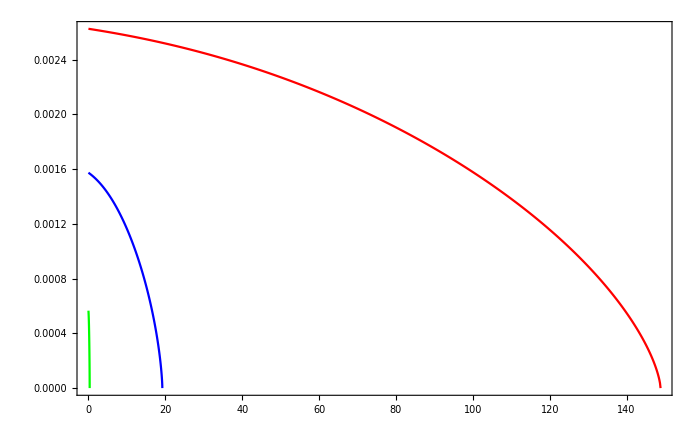

```mathematica
Show[ListPlot[{FractureLength #,Opening}ᵀ/.injectionVertexSolutions["M",paramSet1,#,10^4]&@Range[0,1,0.001],Joined-> True,PlotStyle->Red,PlotLegends->{MaTeX[" t=10\\textsuperscript{4} ",FontSize->Myfontsize-2]}],ListPlot[{FractureLength #,Opening}ᵀ/.injectionVertexSolutions["M",paramSet1,#,10^2]&@Range[0,1,0.001],Joined-> True,PlotStyle->Blue,PlotLegends->{MaTeX[" t=10\\textsuperscript{2} ",FontSize->Myfontsize-2]}],ListPlot[{FractureLength #,Opening}ᵀ/.injectionVertexSolutions["M",paramSet1,#,10^-2]&@Range[0,1,0.001],Joined-> True,PlotStyle->Green,PlotLegends->{MaTeX[" t=10\\textsuperscript{-2} ",FontSize->Myfontsize-2]}],
PlotRange-> All,FrameLabel->{MaTeX["R \\text{ [m]}",FontSize->Myfontsize],MaTeX["w \\text{ [mm]}",FontSize->Myfontsize]}]
```

It is obvius that such A plot is hard to read and merely hids a lot of useful information.

Plotting a Fracture evolution

We can also plot the evolution of a fracture in time. We show an example of such a plot hereafter for the two parameter sets and a toughness dominated fracture evolution.

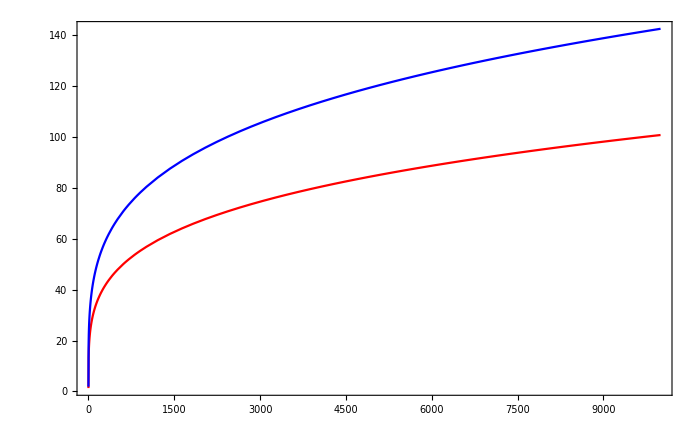

```mathematica
Show[Plot[FractureLength/.injectionVertexSolutions["Mt",paramSet1,.5,t],{t,10^-4,10^4},PlotStyle->Red,PlotLegends->{MaTeX[" \\text{parameter set 1} ",FontSize->Myfontsize-2]}],
Plot[FractureLength/.injectionVertexSolutions["Mt",paramSet2,.5,t],{t,10^-4,10^4},PlotStyle->Blue,PlotLegends->{MaTeX[" \\text{parameter set 2} ",FontSize->Myfontsize-2]}],
PlotRange-> All,FrameLabel->{MaTeX["t \\text{ [s]}",FontSize->Myfontsize],MaTeX["R \\text{ [m]}",FontSize->Myfontsize]}]
```

Note that the near vertex solutions can easily be plotted in the same way.

#### Get the arrest radius of a fracture

There are two arrest radiuses possible for a radial hydraulic fracture, toughness and leak-off arrest.

The toughness arrest radius corresponds to the K-vertex of the pulse solution and can be obtained in two ways: either via the pulse vertex solution or via the arrest radius function

```mathematica
arrestRadius["K",paramSet1]
FractureLength/.pulseVertexSolutions["K",paramSet1,.5,1]
```

37.0755

37.0755

In the leak-off case the radius does not directly correspond to one of the vertex solutions and can thus only be grasped by using the function arrest radius

```mathematica
arrestRadius["Kt",paramSet2]
arrestRadius["Mt",paramSet2]
```

101.945

101.945

Note that the two radiuses are different and that the function arrest radius will return no result for the input “M”.

```mathematica
arrestRadius["Kt",paramSet2]
arrestRadius["K",paramSet2]
```

101.945

56.7941